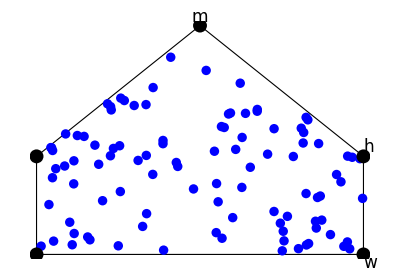

```mathematica
Module[{w,l,h,m,f,getdata,ll,ww,hh},
w=100;l=200;h=30;m=70;

f[x_]:=If[x<w/2,(m-h)/w *2* x+h,(m-h)/w*2*(w-x)+h];

getdata:=(
ww=RandomReal[w,{100}];
hh=RandomReal[f@#]&/@ww;
Transpose[{ww,hh}]);
Graphics[{
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{w,0},{w,h},{w/2,m},{0,h}}]},
{PointSize@0.017,Blue,Point@getdata},
{PointSize@0.025,Point@{{0,0},{w,0},{w,h},{w/2,m},{0,h}}},
Text[Style[#1,17],#2,1.5*#3]&@@@{{"w",{w,0},{-1,1}},{"h",{w,h},{-1,-1}},{"m",{w/2,m},{0,-1}}}
}]
]
```

```mathematica
Manipulate[
Module[{x,y,a1,a2,b,c1,c2,d},
x=1;y=0.5;
a1={{0,2*y},{x,2*y},{x,0}};a2={{0,y},{x-y,y},{x-y,0}};

b[a_]:=Quiet@Interpolation[BezierFunction[a][#]&/@Range[0,x,0.01]];

(*LINES OF BEZIER CURVE*)
c1={#,b[a1][#]}&/@Range[0,x,0.01];
c2={#,b[a2][#]}&/@Range[0,x-y,0.01];

(*d[z_]:=Piecewise[{*)

Graphics[{Thick,
If[bezier,{Blue,BezierCurve@a1,Red,BezierCurve@a2}],
If[lines,{If[bezier,Dashed,Thick],Line@c1,Line@c2}],
Green,Dashed,Line@Join[{{0,y}},c1,{{x-y,0}}],(*Orange,Line@Join[{{0,2*y}},c2,{{x,0}}]*)
}];
Plot[Fit[c1,{1,z,z^2,z^3,z^4},z]/.z->ζ,{ζ,0,x},Epilog->{Thick,Red,Dashed,Line@c1}]
],
Grid@{{
Control[{{bezier,False,"bezier curves"},{True,False}}],
Control[{{lines,True,"lines of bezier curves"},{True,False}}]
}}]
```

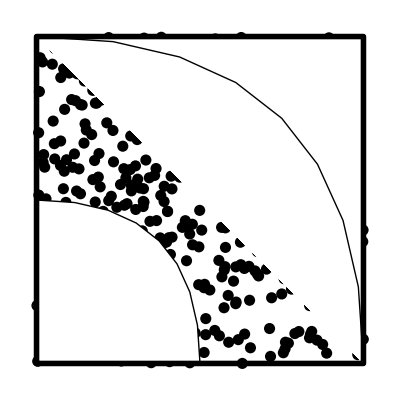

```mathematica
Module[{f1,f2},
f1=BezierCurve[{{0,1},{1,1},{1,0}}];
f2=BezierCurve[Reverse@{{0,0.5},{0.5,0.5},{0.5,0}}];

Graphics[{
PointSize@0.02,Point@RandomPoint[Rectangle[{0,0},{1,1}],500],
{White,FilledCurve[{f1,Line[{{0,1},{1,1},{1,0}}]}],FilledCurve[{f2,Line[{{0,0.5},{0,0},{0.75,0}}]}]},
{Thick,f1,f2},
{EdgeForm@Thickness@0.01,FaceForm@None,Rectangle[{0,0},{1,1}]}
},PlotRangePadding->None]
]
```